```mathematica
Import["ExampleData/rose.gif"]
```

-Graphics-

```mathematica
Import["ExampleData/rose.gif","Elements"]
```

{AnimatedImage,Animation,AnimationRepetitions,Background,BitDepth,Channels,ColorMap,ColorSpace,Comments,Data,DisplayDurations,DisposalOperation,GlobalColorMap,Graphics,GraphicsList,Image,ImageCount,ImageList,ImageSize,RawData,Summary,SummarySlideView,Thumbnail,ThumbnailList,TransparentColor}

```mathematica
Import["ExampleData/rose.gif","SummarySlideView"]
```

```mathematica
Import["http://exampledata.wolfram.com/vase.stl"]
```

-Graphics3D-

```mathematica
Export["landscape.jpg",-Graphics-]
```

landscape.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["landscape.jpg"]]]
```

```mathematica
ImportString["3,4,6\na,b,c","Table"]
```

{{3,4,6},{a,b,c}}

```mathematica
ExportString[RandomReal[10,{4,3}],"Table"]
```

2.4585383541826804	7.090488807496918	1.7983746522376478
5.476605831149195	5.746634925737084	5.527307311439543
3.046450580497904	2.613589281347881	8.307684890100326
4.119006155325485	8.43505327698174	5.997518801788537

```mathematica
Export["grid.dat",{{1, x-1, 2}, {2, (x-1) (x+1), 3}, {3, (x-1) (x^2+x+1), 4}, {4, (x-1) (x+1) (x^2+1), 4}, {5, (x-1) (x^4+x^3+x^2+x+1), 4}, {6, (x-1) (x+1) (x^2-x+1) (x^2+x+1), 6}, {7, (x-1) (x^6+x^5+x^4+x^3+x^2+x+1), 4}}]
```

grid.dat

```mathematica
Import[Export["grid.dat",{{1, x-1, 2}, {2, (x-1) (x+1), 3}, {3, (x-1) (x^2+x+1), 4}, {4, (x-1) (x+1) (x^2+1), 4}, {5, (x-1) (x^4+x^3+x^2+x+1), 4}, {6, (x-1) (x+1) (x^2-x+1) (x^2+x+1), 6}, {7, (x-1) (x^6+x^5+x^4+x^3+x^2+x+1), 4}}]]
```

{{1,-1,+,x,2},{2,(-1,+,x)*(1,+,x),3},{3,(-1,+,x)*(1,+,x,+,x^2),4},{4,(-1,+,x)*(1,+,x)*(1,+,x^2),4},{5,(-1,+,x)*(1,+,x,+,x^2,+,x^3,+,x^4),4},{6,(-1,+,x)*(1,+,x)*(1,-,x,+,x^2)*(1,+,x,+,x^2),6},{7,(-1,+,x)*(1,+,x,+,x^2,+,x^3,+,x^4,+,x^5,+,x^6),4}}

```mathematica
Export["tiger.gif",-Graphics-]
```

tiger.gif

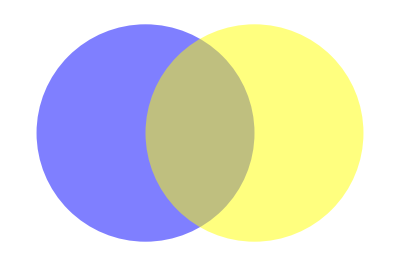

```mathematica
Graphics[{Opacity[0.5],Blue,Disk[],Yellow,Disk[{1,0}]}]
```

```mathematica
Export["disks.svg",%]
```

disks.svg

```mathematica
Import["ExampleData/seashell.ply"]
```

-Graphics3D-

```mathematica
Import["ExampleData/seashell.ply","Summary"]
```

```mathematica
Export["model.ply",-Graphics3D-]
```

model.ply

```mathematica
Export["model.ply",-Graphics3D-,{"PLY","BinaryFormat"-> True}]
```

model.ply

```mathematica
Import[ "ExampleData/rule30.wav" ]
```

```mathematica
Import["ExampleData/Caminandes.mp4"]
```

```mathematica
ImportString["[1,2,3]", "RawJSON"]
```

{1,2,3}

```mathematica
Import["ExampleData/temperatures.json", "RawJSON"]
```

<|01/01/09→-6.06,01/02/09→-2.83,01/03/09→-4.22,01/04/09→1.28,01/05/09→-7.17,01/06/09→-4.83,01/07/09→-2.5,01/08/09→-8.94,01/09/09→-6.78,01/10/09→-2.33,01/11/09→-7.33,01/12/09→-8.11,01/13/09→-8.17,01/14/09→-14.11,01/15/09→-20.11,01/16/09→-23.17,01/17/09→-12.67,01/18/09→-9.22,01/19/09→-9.67,01/20/09→-8.67,01/21/09→-7.94,01/22/09→-5.67,01/23/09→-2.89,01/24/09→-11.78,01/25/09→-15.61,01/26/09→-12.89,01/27/09→-10.72,01/28/09→-9.67,01/29/09→-6.56,01/30/09→-10.61,01/31/09→-7.61|>

```mathematica
ImportString["[1,'h',True,None,1.2]","PythonExpression"]
```

ExternalEvaluate::help: For help configuring the Python evaluator, see Configure Python for ExternalEvaluate.

ExternalEvaluate::noinstall: No valid installations for system Python were found with the options specified.

$Failed

```mathematica
Import[ "ExampleData/buildings.mdb","Elements" ]
```

{Data,Datasets}

```mathematica
Import[ "ExampleData/buildings.mdb",{"Datasets","Buildings","LabeledData",{"Rank","Name","City","Height"}} ]//Transpose // Grid
```

1 | Taipei 101 | Taipei | 508
2 | Petronas Tower 1 | Kuala Lumpur | 452
3 | Petronas Tower 2 | Kuala Lumpur | 452
4 | Sears Tower | Chicago | 442
5 | Jin Mao Building | Shanghai | 421
6 | Two International Finance Centre | Hong Kong | 415
7 | CITIC Plaza | Guangzhou | 391
8 | Shun Hing Square | Shenzhen | 384
9 | Empire State Building | New York | 381
10 | Central Plaza | Hong Kong | 374
11 | Bank of China | Hong Kong | 367
12 | Emirates Tower One | Dubai | 355
13 | Tuntex Sky Tower | Kaohsiung | 348
14 | Aon Centre | Chicago | 346
15 | The Center | Hong Kong | 346
16 | John Hancock Center | Chicago | 344
17 | Shimao International Plaza | Shanghai | 333
18 | Minsheng Bank Building | Wuhan | 331
19 | Ryugyong Hotel | Pyongyang | 330
20 | Q1 | Gold Coast | 323

```mathematica
Needs["GraphStore`"]
```

```mathematica
recipeGraph=ImportString["
PREFIX rdf: <http://www.w3.org/1999/02/22-rdf-syntax-ns#>
PREFIX rdfs: <http://www.w3.org/2000/01/rdf-schema#>
PREFIX time: <http://www.w3.org/2006/time#>
PREFIX fo: <http://purl.org/ontology/fo/>
PREFIX ex: <http://example.org/>

ex:riceWithMushrooms a ex:recipe ;
  rdfs:label \"rice with mushrooms\" ;
  fo:ingredients (ex:rice ex:mushroom ex:oil ex:water ex:salt ex:pepper) ;
  ex:step ex:heatOil ,
    ex:fryMushroom ,
    ex:cookRice ,
    ex:mixRiceAndMushroom .
ex:cookRice time:minutes 10 .
ex:mixRiceAndMushroom time:after ex:fryMushroom ,
  ex:cookRice .
ex:fryMushroom time:after ex:heatOil ;
  time:minutes 7 .
","Turtle"]
```

RDFStore[…]

```mathematica
rdf[s_]:=URL["http://www.w3.org/1999/02/22-rdf-syntax-ns#"<>s];
fo[s_]:=URL["http://purl.org/ontology/fo/"<>s];
ex[s_]:=URL["http://example.org/"<>s];
```

```mathematica
recipeGraph//SPARQLSelect[SPARQLPropertyPath[ex["riceWithMushrooms"],{fo["ingredients"],rdf["rest"]...,rdf["first"]},SPARQLVariable["ingredient"]]]
```

{<|ingredient→URL[http://example.org/rice]|>,<|ingredient→URL[http://example.org/mushroom]|>,<|ingredient→URL[http://example.org/oil]|>,<|ingredient→URL[http://example.org/water]|>,<|ingredient→URL[http://example.org/salt]|>,<|ingredient→URL[http://example.org/pepper]|>}

```mathematica
Import["ExampleData/structured.h5"]
```

{/group1/data1,/group1/linkToGroup2/data}

```mathematica
Import["ExampleData/structured.h5","StructureGraph"]
```

-Graphics-

```mathematica
ListAnimate[TextGrid[#,Frame->All]&/@Import["ExampleData/sample2.h5","/Array"],1]
```

ListAnimate[$Failed,1]

```mathematica
Import["ExampleData/paintings.xml"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Encoding→ISO8859-1]},XMLElement[PAINTINGS,{},{XMLElement[SALE,{},{XMLElement[TITLE,{},{No.5, 1948}],XMLElement[ARTIST,{},{Jackson Pollock}],XMLElement[YEAR,{},{1948}],XMLElement[PRICE,{},{$140,000,000}]}],XMLElement[SALE,{},{XMLElement[TITLE,{},{Woman III}],XMLElement[ARTIST,{},{Willem de Kooning}],XMLElement[YEAR,{},{1953}],XMLElement[PRICE,{},{$137,500,000}]}],XMLElement[SALE,{},{XMLElement[TITLE,{},{Portrait of Adele Block-Bauer I}],XMLElement[ARTIST,{},{Gustav Klimt}],XMLElement[YEAR,{},{1907}],XMLElement[PRICE,{},{$135,000,000}]}],XMLElement[SALE,{},{XMLElement[TITLE,{},{Portrait of Dr. Gachet}],XMLElement[ARTIST,{},{Vincent van Gogh}],XMLElement[YEAR,{},{1890}],XMLElement[PRICE,{},{$82,500,000}]}],XMLElement[SALE,{},{XMLElement[TITLE,{},{Bal au moulin de la Galette, Montmartre}],XMLElement[ARTIST,{},{Pierre-Auguste Renoir}],XMLElement[YEAR,{},{1876}],XMLElement[PRICE,{},{$78,100,000}]}]}],{}]

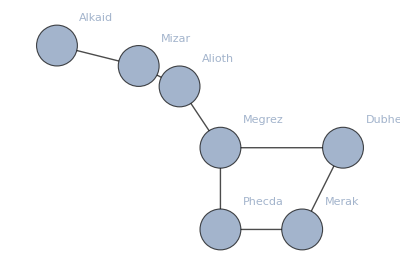

```mathematica
Import["ExampleData/bigdipper.gml",ImagePadding->10]
```

```mathematica
Export["response.txt",HTTPRequest[…],"HTTPRequest"]
```

response.txt

```mathematica
Import["ExampleData/Collatz.m", "Elements"]
```

{Comments,ExpressionList,ExprStructs,HeldExpressions,InactivatedExpressions}

```mathematica
Import["ExampleData/Collatz.m", "HeldExpressions"]
```

{HoldComplete[BeginPackage[Collatz`]],HoldComplete[Collatz::usage=Collatz[n] gives a list of the iterates in the 3n+1 problem,
        starting from n. The conjecture is that this sequence always
        terminates.],HoldComplete[Begin[`Private`]],HoldComplete[Collatz[1]:={1}],HoldComplete[Collatz[n_Integer]:=Prepend[Collatz[3 n+1],n]/;OddQ[n]&&n>0],HoldComplete[Collatz[n_Integer]:=Prepend[Collatz[n/2],n]/;EvenQ[n]&&n>0],HoldComplete[End[]],HoldComplete[EndPackage[]]}

```mathematica
Import["ExampleData/Collatz.m", "InactivatedExpressions"]
```

{BeginPackage[Collatz`],MessageName[Collatz,usage]=Collatz[n] gives a list of the iterates in the 3n+1 problem,
        starting from n. The conjecture is that this sequence always
        terminates.,Begin[`Private`],Collatz[1]:={1},Collatz[n_Integer]:=Condition[Prepend[Collatz[3×n+1],n],OddQ[n]&&n>0],Collatz[n_Integer]:=Condition[Prepend[Collatz[n×2^(-1)],n],EvenQ[n]&&n>0],End[],EndPackage[]}

```mathematica
ImportString["1+5", {"WL", "ExprStructs", 1}]
```

DataStructure[…]

```mathematica
Import["ExampleData/attach.eml"]
```

<|From→Alice Johnson <alice@docex.wolfram.com>,FromAddress→alice@docex.wolfram.com,FromName→Alice Johnson,ToList→{Eve Anderson <eve@docex.wolfram.com>},ToAddressList→{eve@docex.wolfram.com},ToNameList→{Eve Anderson},CcList→{Bob Doe <bob@docex.wolfram.com>,Trent Jones <trent@docex.wolfram.com>},CcAddressList→{bob@docex.wolfram.com,trent@docex.wolfram.com},CcNameList→{Bob Doe,Trent Jones},BccList→{Frank Brown <frank@docex.wolfram.com>},BccAddressList→{frank@docex.wolfram.com},BccNameList→{Frank Brown},ReplyToList→{Alice Johnson <alice@docex.wolfram.com>},ReplyToAddressList→{alice@docex.wolfram.com},ReplyToNameList→{Alice Johnson},OriginatingDate→Thu 12 May 2016 12:33:46GMT-5,Subject→Wolfram Language Functions,Body→Eve,

I've been playing with the Wolfram Language functions Import and Export. 
I'd like to see what I can do once I've imported these files. Do you 
have any suggestions?

Thanks,

Alice

,AttachmentList→{,-Graphics-},MessageID→<2955d7e5-7eeb-ba29-a94e-5638d856c732@docex.wolfram.com>|>

```mathematica
Import["ExampleData/in.mbox"]
```

{<|From→"John Doe" <johndoe@docex.wolfram.com>,ToList→{"'Jane Roe'" <jane@docex.wolfram.com>},CcList→{},BccList→{},OriginatingDate→Wed 14 Mar 2007 11:55:47GMT-6,Subject→Hello,BodyPreview→This is just a test.,HasAttachments→False,MessageID→<200703141655.l2EGtfL3002494@docex.wolfram.com>|>,<|From→"John Doe" <johndoe@docex.wolfram.com>,ToList→{"'Jane Roe'" <jane@docex.wolfram.com>},CcList→{},BccList→{},OriginatingDate→Wed 14 Mar 2007 11:55:50GMT-6,Subject→swan picture,BodyPreview→Here's the photo ...,HasAttachments→True,MessageID→<200703141655.l2EGtfL4002494@docex.wolfram.com>|>}

```mathematica
maxSize=Max@@Lookup[#,"ByteCount",0]&/@Import["ExampleData/conv.mbox","AttachmentSummaries"]
```

{113240,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Import["ExampleData/conv.mbox",{"MessageElements",#}]&/@Flatten[Position[ maxSize,d_/;d>50000]]
```

{<|From→Alice Johnson <alice@docex.wolfram.com>,FromAddress→alice@docex.wolfram.com,FromName→Alice Johnson,ToList→{Bob Doe <bob@docex.wolfram.com>},ToAddressList→{bob@docex.wolfram.com},ToNameList→{Bob Doe},CcList→{Eve Anderson <eve@docex.wolfram.com>,Trent Jones <trent@docex.wolfram.com>},CcAddressList→{eve@docex.wolfram.com,trent@docex.wolfram.com},CcNameList→{Eve Anderson,Trent Jones},BccList→{},BccAddressList→{},BccNameList→{},ReplyToList→{Alice Johnson <alice@docex.wolfram.com>},ReplyToAddressList→{alice@docex.wolfram.com},ReplyToNameList→{Alice Johnson},OriginatingDate→Thu 12 May 2016 12:33:46GMT-5,Subject→Good morning!,Body→Hi Bob,

How was the weather when you got to the office this morning?

What do you think of this picture of a swan?

Thanks,

Alice

,AttachmentList→{-Graphics-},MessageID→<2955d7e5-7eeb-ba29-a94e-5638d856c732@docex.wolfram.com>|>}

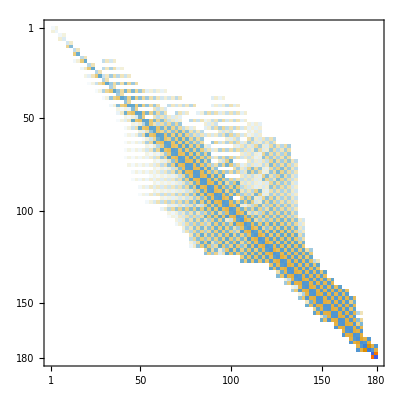

```mathematica
Import["ExampleData/mcca.rua.gz", "Graphics"]
```

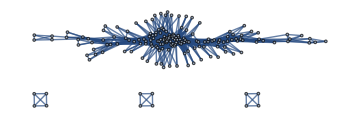

```mathematica
GraphPlot[ Import["ExampleData/mcca.rua.gz"] , ImageSize->Medium]
```

## Import

```mathematica
$ImportFormats
```

{3DS,7z,ACO,Affymetrix,AgilentMicroarray,AIFF,ApacheLog,ArcGRID,AU,AVI,Base64,BDF,Binary,BioImageFormat,Bit,BMP,BSON,Byte,BYU,BZIP2,CDED,CDF,CDX,CDXML,Character16,Character32,Character8,CIF,CML,Complex128,Complex256,Complex64,CSV,Cube,CUR,DAE,DBF,DICOM,DICOMDIR,DIF,DIMACS,Directory,DOT,DTA,DXF,EDF,EML,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FBX,FCHK,FCS,FITS,FLAC,FLV,GaussianLog,GenBank,GeoJSON,GeoTIFF,GIF,GPX,Graph6,Graphlet,GraphML,GRIB,GTOPO30,GXL,GZIP,HarwellBoeing,HDF,HDF5,HEIF,HIN,HTML,HTTPRequest,HTTPResponse,ICC,ICNS,ICO,ICS,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,ISO,JavaProperties,JavaScriptExpression,JCAMP-DX,JPEG,JPEG2000,JSON,JSONLD,JVX,KML,LaTeX,LEDA,List,LWO,MAT,MathML,Matroska,MBOX,MCTT,MDB,MESH,MGF,MIDI,MMCIF,MO,MOL,MOL2,MP3,MP4,MPS,MTP,MTX,MX,MXNet,NASACDF,NB,NDK,NetCDF,NEXUS,NOFF,NQuads,NTriples,OBJ,ODS,OFF,Ogg,ONNX,OpenEXR,OWLFunctional,Pajek,PBM,PCAP,PCX,PDB,PDF,PEM,PGM,PHPIni,PLY,PNG,PNM,POR,PPM,PXR,PythonExpression,QuickTime,RAR,Raw,RawBitmap,RawJSON,RDFXML,Real128,Real32,Real64,RIB,RLE,RSS,RTF,SAS7BDAT,SAV,SCT,SDF,SDTS,SDTSDEM,SFF,SHP,SMA,SME,SMILES,SND,SP3,SPARQLQuery,SPARQLResultsJSON,SPARQLResultsXML,SPARQLUpdate,Sparse6,STL,String,SurferGrid,SXC,Table,TAR,TerminatedString,TeX,Text,TGA,TGF,TIFF,TIGER,TLE,TriG,TSV,Turtle,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,USGSDEM,UUE,VCF,VCS,VideoFormat,VTK,WARC,WAV,Wave64,WDX,WebP,WL,WLNet,WMLF,WXF,X3D,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP,ZSTD,$Failed}

Import a “GIF” file with a rose:

```mathematica
Import["ExampleData/rose.gif"]
```

-Graphics-

Find what elements are in the file:

```mathematica
Import["ExampleData/rose.gif","Elements"]
```

{AnimatedImage,Animation,AnimationRepetitions,Background,BitDepth,Channels,ColorMap,ColorSpace,Comments,Data,DisplayDurations,DisposalOperation,GlobalColorMap,Graphics,GraphicsList,Image,ImageCount,ImageList,ImageSize,RawData,Summary,SummarySlideView,Thumbnail,ThumbnailList,TransparentColor}

```mathematica
AssociationMap[Import["ExampleData/rose.gif",#]&,Import["ExampleData/rose.gif","Elements"]]
```

```mathematica
<|"AnimatedImage"->,"Animation"->,"AnimationRepetitions"->1,"Background"->RGBColor[0., 0.03137254901960784, 0.],"BitDepth"->8,"Channels"->3,"ColorMap"->None,"ColorSpace"->"RGB","Comments"->None,"Data"->{,{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{90,115,99},{165,173,165},{255,255,255},{247,247,231},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{148,165,156},{66,82,74},{198,189,189},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{123,140,132},{66,82,74},{33,41,33},{198,206,198},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{148,165,140},{66,90,57},{66,90,57},{148,165,140},{247,247,247},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{148,165,156},{66,90,57},{66,66,41},{49,74,49},{231,239,239},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{140,148,140},{66,90,57},{66,74,57},{66,74,57},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{123,132,107},{66,90,57},{33,41,16},{41,49,33},{181,189,189},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{231,239,239},{49,82,57},{41,66,41},{33,41,16},{33,66,33},{66,90,57},{173,181,173},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{231,239,239},{255,255,255},{41,66,41},{41,66,41},{66,74,57},{33,57,16},{41,66,41},{140,148,140},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,247},{24,41,33},{41,49,33},{66,90,57},{33,57,16},{16,41,16},{148,165,156},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{189,189,173},{16,41,16},{41,49,33},{49,82,41},{33,57,16},{49,82,41},{115,115,90},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{41,66,41},{66,66,41},{49,82,41},{49,74,49},{49,74,33},{33,57,16},{33,66,33},{247,247,247},{231,239,239},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{49,49,41},{41,66,41},{49,74,33},{66,66,41},{33,66,33},{33,41,16},{33,57,16},{231,239,239},{247,247,247},{247,247,247},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{24,41,33},{41,49,33},{41,66,41},{66,74,41},{49,74,33},{33,57,16},{24,57,33},{82,90,82},{247,247,247},{247,247,247},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{24,41,33},{24,57,33},{33,66,33},{66,74,41},{49,74,33},{33,57,16},{41,66,41},{16,33,16},{231,239,239},{231,239,239},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{231,239,239},{33,41,33},{66,66,41},{33,57,16},{49,82,41},{66,90,41},{33,57,16},{66,90,41},{24,57,33},{173,181,173},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{231,231,214},{33,41,16},{33,57,16},{49,74,33},{49,74,33},{24,49,0},{24,49,0},{49,74,33},{8,41,0},{82,90,74},{231,239,239},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{231,231,231},{99,107,57},{49,74,33},{33,57,16},{33,57,16},{24,49,0},{33,57,16},{33,57,16},{66,90,41},{33,57,16},{49,82,41},{173,181,173},{123,140,123},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{214,206,206},{0,8,0},{24,49,0},{66,90,41},{24,49,0},{33,57,16},{24,49,0},{33,57,16},{24,49,0},{33,57,16},{8,41,0},{8,41,0},{33,57,16},{82,90,82},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{173,181,173},{33,57,16},{24,49,0},{33,57,16},{33,57,16},{49,74,33},{49,74,33},{74,66,24},{33,57,16},{74,66,24},{49,74,33},{49,74,33},{33,57,16},{49,74,33},{49,74,33},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{189,189,173},{33,66,33},{33,57,16},{49,74,33},{33,57,16},{33,57,16},{49,74,33},{49,74,33},{33,57,16},{49,74,33},{49,74,33},{49,74,33},{33,57,16},{33,57,16},{49,74,33},{49,82,57},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{41,66,41},{24,49,0},{24,49,0},{49,74,33},{49,74,33},{49,74,33},{49,74,33},{33,57,16},{33,57,16},{33,57,16},{33,57,16},{49,74,33},{33,57,16},{33,57,16},{33,57,16},{49,74,33},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{198,189,189},{33,41,16},{33,57,16},{49,74,33},{33,57,16},{33,57,16},{49,74,33},{49,74,33},{49,74,33},{49,74,33},{49,74,33},{49,74,33},{49,74,33},{33,57,16},{49,74,33},{33,57,16},{33,57,16},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{231,239,239},{198,214,206},{33,57,16},{33,57,16},{33,57,16},{49,74,33},{49,74,33},{49,74,33},{49,74,33},{33,57,16},{66,90,41},{33,57,16},{33,57,16},{49,74,33},{49,74,33},{66,90,41},{33,57,16},{33,57,16},{115,115,90},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,231},{255,255,255},{123,140,123},{41,66,41},{33,57,16},{49,74,33},{33,57,16},{49,74,33},{49,74,33},{49,74,33},{33,57,16},{66,90,41},{49,74,33},{49,74,33},{49,74,33},{49,74,33},{66,90,41},{66,90,41},{33,57,16},{49,41,33},{247,247,247},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{231,231,231},{255,255,255},{66,82,74},{66,90,57},{24,49,0},{33,57,16},{49,74,33},{33,57,16},{49,74,33},{33,57,16},{49,74,33},{49,74,33},{49,74,33},{33,57,16},{24,49,0},{24,49,0},{24,49,0},{99,82,41},{132,107,82},{173,148,123},{231,206,189},{231,222,198},{231,222,198},{247,231,214},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,231},{231,239,239},{41,49,41},{33,57,16},{49,74,33},{49,74,33},{74,66,24},{66,90,41},{49,74,33},{49,74,33},{49,74,33},{49,74,33},{66,90,41},{99,107,57},{115,115,74},{198,181,148},{247,214,173},{247,214,173},{222,206,165},{222,181,148},{247,206,173},{222,181,148},{222,181,148},{222,198,165},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{8,41,0},{49,74,33},{49,74,33},{49,74,33},{49,74,33},{74,66,24},{24,49,0},{74,66,24},{24,49,0},{115,115,74},{198,189,165},{214,222,198},{231,222,198},{247,214,173},{247,189,156},{222,181,148},{222,198,165},{222,181,148},{222,181,148},{214,173,132},{214,173,132},{214,173,132},{231,231,214},{255,255,255},{247,247,231},{247,231,214},{247,214,198},{247,214,198},{231,214,206},{231,206,189},{222,206,173},{222,198,165},{222,198,165},{198,189,173},{247,247,247},{255,255,255},{247,247,231},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{33,57,16},{33,57,16},{66,90,41},{24,49,0},{24,49,0},{74,66,24},{115,115,74},{222,198,148},{247,247,206},{198,165,115},{222,206,165},{222,198,148},{222,198,165},{247,214,189},{222,181,148},{165,140,115},{198,165,132},{222,181,148},{222,181,148},{222,181,148},{222,181,148},{222,198,165},{222,181,148},{222,198,165},{222,198,165},{247,206,173},{247,206,173},{247,206,173},{247,189,156},{222,181,148},{222,181,148},{222,173,132},{198,165,132},{198,165,132},{222,198,165},{247,231,214},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,231,231},{66,66,41},{66,41,8},{74,66,24},{148,132,90},{222,206,165},{247,247,206},{222,206,165},{247,214,173},{247,231,189},{222,181,148},{247,189,156},{247,214,189},{247,206,173},{247,206,173},{247,206,173},{247,206,173},{247,206,173},{247,206,173},{231,206,189},{247,214,189},{247,214,189},{247,214,189},{247,214,173},{247,214,173},{247,214,173},{247,189,156},{247,189,156},{222,198,148},{222,181,132},{222,173,132},{214,173,132},{214,173,132},{198,165,132},{222,156,115},{198,165,115},{222,206,173},{214,206,189},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{107,115,107},{148,132,123},{247,231,189},{231,206,189},{247,214,173},{222,206,173},{222,206,173},{247,206,156},{247,189,156},{222,181,148},{247,214,198},{247,206,173},{247,214,189},{247,189,156},{222,206,173},{247,206,173},{247,214,173},{247,206,173},{247,214,189},{247,214,189},{247,214,189},{247,206,173},{247,206,173},{247,206,173},{247,214,173},{247,206,173},{247,206,173},{222,198,148},{222,181,148},{222,181,148},{198,165,132},{198,165,115},{198,165,115},{189,148,115},{214,156,115},{198,140,82},{247,189,148},{198,148,115},{231,231,231},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{247,247,247},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,247},{255,255,255},{247,247,247},{255,255,255},{247,247,247},{247,247,247},{247,231,231},{247,231,231},{231,206,189},{222,198,165},{222,206,173},{222,206,173},{222,206,173},{231,206,189},{231,206,189},{231,206,189},{247,189,156},{198,165,132},{222,181,148},{222,173,132},{222,181,148},{247,206,156},{222,198,148},{247,206,156},{247,189,156},{247,189,156},{247,206,156},{247,206,156},{247,206,173},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{222,198,165},{222,181,148},{198,181,148},{198,165,132},{198,165,132},{198,165,115},{198,165,115},{198,165,115},{198,165,115},{198,165,132},{198,165,115},{214,173,132},{222,181,148},{222,181,148},{231,206,189},{247,247,247},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,231,231},{231,231,231},{247,247,247},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,231},{231,231,214},{247,231,214},{222,198,165},{222,181,148},{222,181,148},{222,198,165},{247,206,173},{231,206,189},{231,206,189},{247,214,189},{247,214,173},{247,214,173},{222,206,173},{222,206,173},{222,181,148},{214,156,115},{222,173,132},{189,165,148},{214,173,132},{222,181,148},{222,181,132},{214,173,132},{222,181,132},{222,181,148},{222,181,148},{214,173,132},{222,181,148},{222,181,148},{222,181,148},{222,181,148},{222,181,148},{222,181,148},{222,181,148},{198,165,132},{214,173,132},{198,165,115},{198,165,115},{198,165,115},{198,148,115},{189,148,115},{173,148,123},{189,148,115},{198,165,132},{198,165,115},{222,181,148},{222,181,148},{222,181,148},{214,206,206},{247,247,247},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{181,189,189},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,231},{247,247,231},{247,231,231},{198,189,189},{198,189,173},{222,198,165},{222,198,165},{198,189,189},{214,206,189},{247,206,173},{247,214,189},{247,206,173},{247,189,156},{247,206,173},{247,206,173},{247,206,173},{247,206,173},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{214,173,132},{214,156,115},{214,156,115},{198,165,132},{222,156,115},{214,173,132},{222,181,148},{222,173,132},{214,173,132},{222,173,132},{247,189,148},{247,206,156},{222,181,148},{222,181,148},{222,181,132},{222,181,148},{222,173,132},{214,156,115},{214,156,115},{214,173,132},{214,173,132},{198,165,115},{198,148,115},{198,165,115},{198,148,115},{198,165,115},{198,165,115},{198,165,115},{198,165,115},{198,165,115},{198,165,132},{222,181,132},{222,181,148},{198,181,148},{222,198,165},{247,231,214},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,231,231},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,231},{189,189,173},{132,123,90},{173,156,148},{198,173,165},{247,231,189},{231,206,189},{247,189,156},{247,189,156},{247,189,156},{231,206,189},{231,206,189},{222,198,165},{231,206,189},{247,214,189},{247,214,189},{222,206,173},{222,206,165},{222,198,148},{247,206,156},{247,206,156},{222,181,148},{222,181,148},{222,181,148},{222,156,115},{198,165,132},{198,165,132},{214,173,132},{198,165,115},{214,173,132},{198,165,115},{214,156,115},{214,156,115},{198,148,115},{173,140,99},{222,181,148},{198,148,115},{214,156,115},{198,165,132},{214,173,132},{222,156,115},{198,165,115},{198,165,115},{198,148,99},{198,148,99},{198,148,99},{189,148,115},{198,148,99},{198,148,99},{198,165,115},{214,173,132},{198,148,99},{198,165,115},{198,165,132},{198,165,115},{222,173,115},{222,198,148},{222,198,148},{222,181,148},{247,247,231},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{90,90,90},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,231,214},{198,165,115},{173,107,57},{247,206,156},{247,206,156},{247,206,173},{247,189,156},{222,181,148},{222,181,148},{222,198,165},{222,181,148},{222,198,165},{222,198,165},{231,206,189},{231,206,189},{222,198,165},{222,206,165},{222,206,165},{222,181,148},{222,181,148},{222,181,132},{222,181,148},{198,165,132},{214,173,132},{214,173,132},{214,173,132},{198,148,115},{198,165,132},{198,148,99},{198,165,132},{198,165,132},{198,148,115},{214,156,115},{222,156,115},{198,165,132},{198,165,115},{198,148,115},{222,156,115},{222,156,115},{214,156,115},{214,156,115},{198,165,132},{214,156,115},{198,148,115},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{214,173,132},{198,148,99},{214,156,99},{222,173,115},{198,148,99},{247,214,173},{198,165,132},{222,181,148},{247,214,173},{247,247,231},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,247},{214,206,206},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{222,206,173},{198,165,115},{198,140,82},{198,165,115},{214,173,132},{247,189,156},{222,181,148},{222,181,148},{198,173,165},{222,181,148},{247,189,156},{247,189,156},{247,189,156},{198,173,165},{222,198,165},{222,181,148},{222,181,148},{222,181,132},{222,181,132},{198,165,132},{214,173,132},{222,181,132},{214,173,132},{214,173,132},{222,173,132},{214,156,115},{198,148,115},{214,156,115},{214,156,115},{214,156,115},{173,140,99},{198,165,115},{198,148,115},{198,148,115},{198,165,132},{198,148,115},{198,148,99},{198,148,99},{198,148,99},{198,148,115},{214,156,115},{198,148,99},{214,140,99},{214,156,99},{214,140,99},{214,156,99},{214,156,99},{198,148,99},{214,156,99},{214,156,99},{214,156,99},{214,156,99},{214,156,99},{222,173,115},{181,140,99},{198,148,99},{222,156,115},{247,214,173},{222,181,132},{222,198,148},{247,189,148},{247,247,231},{247,247,247},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{140,148,140},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{189,165,148},{181,140,99},{173,123,57},{214,156,115},{181,140,99},{222,181,132},{181,140,99},{222,181,148},{198,181,148},{198,181,148},{222,181,148},{222,181,148},{214,173,132},{222,181,148},{222,181,148},{222,181,132},{214,173,132},{214,173,132},{222,156,115},{222,156,115},{247,189,148},{222,181,132},{222,181,148},{222,173,132},{214,173,132},{198,165,115},{198,165,115},{198,148,115},{198,165,115},{198,148,115},{198,148,99},{214,156,115},{198,148,115},{198,148,115},{198,148,115},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{198,140,82},{198,148,99},{198,148,99},{214,156,99},{214,140,99},{214,156,99},{214,156,99},{214,148,82},{214,148,82},{214,156,99},{231,156,82},{214,156,99},{214,156,99},{214,156,99},{231,165,99},{214,156,99},{214,156,99},{214,173,132},{239,173,132},{222,173,115},{222,198,148},{222,181,132},{247,206,173},{247,231,214},{247,247,231},{255,255,255},{247,247,247},{255,255,255},{107,115,107},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{189,165,148},{198,148,99},{173,132,82},{148,107,66},{214,156,115},{181,140,99},{222,156,115},{189,148,115},{198,148,115},{214,173,132},{198,148,115},{198,165,132},{222,181,148},{214,173,132},{198,148,99},{214,173,132},{214,156,99},{198,165,115},{214,156,115},{222,156,115},{247,189,148},{222,181,148},{239,173,132},{222,173,132},{214,156,115},{214,173,132},{198,148,115},{198,148,115},{198,165,115},{198,148,115},{198,165,115},{214,156,115},{198,148,115},{198,148,115},{198,148,99},{214,156,99},{214,156,99},{198,165,115},{198,148,99},{198,148,99},{214,156,99},{214,156,99},{214,148,82},{214,148,82},{214,148,82},{214,148,82},{214,156,99},{231,156,82},{231,156,82},{231,156,82},{231,165,99},{231,165,99},{214,148,82},{214,156,99},{231,165,99},{222,173,115},{222,156,99},{214,156,115},{222,181,132},{247,189,132},{247,206,156},{222,181,148},{222,181,148},{247,231,231},{255,255,255},{247,247,247},{255,255,255},{181,189,189},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{231,239,239},{214,222,214},{231,231,231},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{173,148,123},{198,165,115},{165,123,82},{173,132,82},{198,148,99},{198,165,115},{173,140,99},{198,165,132},{198,165,115},{198,165,132},{198,165,132},{198,165,132},{198,165,132},{222,156,115},{198,165,115},{214,173,132},{198,148,99},{198,148,99},{173,132,82},{222,173,132},{247,189,148},{247,189,148},{239,173,132},{214,173,132},{222,156,115},{222,181,148},{214,156,115},{198,148,115},{198,148,99},{198,148,115},{214,156,115},{214,156,115},{198,165,115},{198,148,115},{198,148,99},{198,148,99},{214,148,82},{214,148,82},{214,148,82},{214,148,82},{214,148,82},{214,148,82},{214,148,82},{214,156,99},{214,156,99},{214,148,82},{214,148,82},{231,156,82},{214,148,82},{247,173,99},{231,165,99},{214,156,99},{214,156,99},{231,165,99},{231,165,99},{214,156,99},{222,156,99},{222,156,99},{231,165,99},{222,173,115},{222,181,132},{222,181,132},{222,181,148},{222,198,165},{247,231,214},{247,247,247},{148,132,123},{198,189,189},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,231,231},{247,231,206},{247,206,173},{222,198,165},{214,173,132},{198,165,115},{222,181,132},{222,181,148},{231,222,198},{247,247,231},{247,247,247},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{198,165,115},{214,173,132},{173,148,123},{173,140,99},{198,148,99},{198,148,99},{173,140,99},{198,148,115},{198,165,132},{198,165,115},{198,165,132},{189,148,115},{198,148,115},{198,148,115},{198,148,99},{198,148,99},{222,173,115},{173,132,82},{198,165,115},{222,181,132},{222,181,132},{222,181,132},{222,173,132},{222,173,132},{222,156,115},{214,156,115},{214,156,115},{222,156,115},{222,173,132},{214,156,115},{198,148,99},{214,156,99},{214,156,99},{198,148,99},{198,148,99},{198,148,99},{214,148,82},{231,156,82},{231,156,82},{231,156,82},{214,132,57},{231,156,82},{231,156,82},{231,156,82},{231,156,82},{231,156,82},{247,165,82},{247,173,99},{247,173,99},{247,173,99},{231,165,99},{231,165,99},{214,156,99},{231,165,99},{231,156,82},{231,156,82},{231,165,99},{231,165,99},{231,165,99},{231,165,99},{222,156,99},{222,181,132},{247,189,148},{214,173,132},{222,206,173},{247,231,206},{66,74,57},{247,247,231},{231,239,239},{255,255,255},{247,247,247},{247,231,231},{247,231,214},{247,231,206},{247,189,156},{247,189,156},{247,189,132},{222,181,132},{214,173,132},{214,173,132},{198,165,132},{222,181,148},{222,181,132},{247,214,173},{247,231,231},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{198,165,132},{198,165,132},{173,140,99},{173,140,99},{198,165,115},{198,165,115},{198,165,115},{198,148,115},{198,148,115},{198,148,115},{198,165,115},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{247,206,156},{222,181,148},{222,181,132},{222,181,132},{222,181,132},{222,173,115},{222,156,115},{214,156,115},{214,156,115},{222,156,115},{198,148,99},{214,156,99},{222,156,99},{214,140,99},{214,140,99},{214,156,99},{214,156,99},{214,148,82},{214,148,82},{231,156,82},{231,156,82},{231,156,82},{239,148,57},{239,148,57},{231,156,82},{247,165,82},{231,156,82},{247,165,82},{231,156,82},{247,173,99},{247,173,99},{247,165,82},{231,156,82},{247,165,82},{231,156,82},{214,148,82},{231,156,82},{231,156,82},{231,156,82},{231,156,82},{231,165,99},{214,148,82},{222,173,115},{222,173,115},{222,181,132},{247,189,132},{247,189,148},{222,198,148},{198,165,132},{222,206,173},{231,206,189},{222,198,165},{247,206,173},{247,214,189},{247,206,156},{247,189,148},{247,189,132},{222,181,132},{222,173,115},{222,173,115},{214,173,132},{198,165,115},{198,165,115},{198,165,132},{214,173,132},{222,181,148},{222,181,148},{222,198,165},{247,231,231},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{189,148,115},{214,173,132},{198,165,132},{198,165,132},{198,165,115},{198,148,115},{189,148,115},{198,165,132},{198,165,132},{198,148,115},{189,148,115},{173,148,123},{198,148,99},{198,148,99},{198,148,99},{198,165,115},{198,140,82},{222,173,115},{222,181,132},{222,181,148},{222,181,132},{222,181,132},{222,181,132},{222,173,115},{222,156,115},{214,156,99},{214,173,132},{222,156,115},{222,156,99},{222,173,115},{198,140,82},{214,156,99},{214,140,99},{222,156,99},{222,156,99},{214,156,99},{214,148,82},{231,156,82},{214,132,57},{231,156,82},{214,148,82},{239,148,57},{247,165,82},{247,165,82},{247,165,82},{247,165,82},{247,165,82},{231,165,99},{247,165,82},{247,173,99},{231,156,82},{247,165,82},{247,189,132},{247,165,82},{239,148,57},{239,148,57},{239,148,57},{231,156,82},{214,148,82},{231,165,99},{247,189,132},{231,165,99},{214,156,99},{222,173,115},{247,189,132},{247,189,132},{247,206,156},{247,206,156},{247,206,156},{247,231,189},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{222,181,132},{222,181,132},{222,181,132},{222,181,132},{222,181,132},{214,173,132},{214,173,132},{198,148,115},{214,173,132},{222,181,148},{247,189,148},{247,206,156},{222,206,165},{222,206,173},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{231,231,214},{198,181,148},{189,148,115},{189,165,148},{198,165,132},{173,140,99},{198,165,115},{198,148,99},{189,148,115},{189,148,115},{198,148,99},{198,148,99},{198,148,115},{198,148,99},{198,148,99},{198,140,82},{198,140,82},{214,156,99},{247,189,148},{222,181,132},{222,181,132},{222,181,132},{222,181,132},{222,181,132},{222,156,115},{222,173,115},{214,156,99},{214,156,99},{222,156,115},{222,156,99},{222,156,115},{222,156,99},{214,148,82},{214,156,99},{231,156,82},{231,140,82},{231,156,82},{231,140,74},{231,156,82},{231,140,57},{231,140,57},{214,132,57},{247,165,82},{239,148,57},{239,148,57},{247,165,82},{231,156,82},{231,156,82},{247,165,82},{247,165,82},{247,165,82},{247,165,82},{231,156,82},{231,156,82},{231,156,82},{247,165,82},{231,156,82},{231,156,82},{239,148,57},{239,148,57},{231,156,82},{231,156,82},{231,165,99},{231,165,99},{247,189,132},{247,206,156},{247,206,156},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{222,198,148},{247,189,132},{222,181,132},{247,189,132},{222,181,132},{247,189,132},{198,165,115},{222,181,132},{198,165,115},{198,165,132},{247,206,156},{214,173,132},{198,148,115},{189,148,115},{247,214,173},{247,206,156},{247,214,173},{231,206,189},{247,247,231},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{231,222,198},{189,165,132},{189,148,115},{189,148,115},{247,247,206},{165,140,99},{189,148,115},{198,165,115},{198,148,99},{198,148,115},{189,148,115},{181,140,99},{198,148,99},{198,148,99},{198,148,99},{198,140,82},{198,140,82},{214,156,99},{247,189,148},{222,173,115},{222,181,148},{222,173,132},{222,173,115},{222,173,115},{222,173,115},{222,173,115},{222,173,115},{222,156,115},{231,165,99},{231,165,99},{231,140,82},{231,156,82},{214,148,82},{231,156,82},{214,132,82},{214,148,82},{231,156,82},{231,156,82},{239,148,57},{239,148,57},{231,156,82},{247,165,82},{247,165,82},{247,173,99},{247,165,82},{247,165,82},{247,165,82},{247,173,99},{247,173,99},{247,173,99},{247,165,82},{247,165,82},{247,165,82},{247,165,82},{231,156,82},{214,148,82},{239,148,57},{247,165,82},{247,165,82},{239,148,57},{239,148,57},{231,156,82},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,173,99},{247,189,132},{247,189,132},{222,181,132},{222,173,115},{222,181,132},{222,173,115},{222,173,115},{222,173,115},{222,181,132},{214,173,132},{198,165,115},{214,156,115},{222,181,148},{181,140,99},{173,140,99},{222,181,148},{222,206,173},{198,165,132},{247,214,173},{222,181,148},{247,231,214},{247,247,231},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{231,222,198},{198,165,132},{198,148,115},{173,140,99},{247,206,173},{165,140,99},{165,140,99},{214,173,132},{189,148,115},{198,148,99},{198,148,99},{173,132,82},{198,140,82},{198,140,82},{214,132,82},{214,156,99},{214,148,82},{247,189,132},{247,189,132},{214,173,132},{247,189,148},{222,181,148},{222,156,115},{222,173,115},{222,173,115},{222,156,115},{222,156,99},{214,156,99},{214,156,99},{214,148,82},{214,140,99},{214,148,82},{247,189,132},{247,189,132},{247,173,99},{239,148,99},{231,156,82},{231,156,82},{247,148,82},{247,148,57},{239,148,57},{247,165,82},{239,148,57},{247,165,82},{247,165,82},{247,165,82},{247,165,82},{247,165,82},{247,173,99},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{222,173,115},{198,165,115},{189,132,57},{189,132,57},{239,148,57},{247,165,82},{247,189,132},{247,165,82},{247,173,99},{247,173,99},{247,189,132},{247,189,132},{222,173,115},{247,173,99},{222,173,115},{231,165,99},{222,181,132},{222,173,115},{222,173,115},{222,173,115},{222,173,115},{222,181,132},{214,173,132},{222,181,132},{214,156,115},{198,148,115},{222,181,148},{214,173,132},{222,181,148},{198,165,115},{247,214,189},{214,156,115},{198,165,132},{247,214,173},{222,181,148},{247,214,173},{247,214,173},{247,231,206},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{214,206,189},{189,165,132},{198,165,132},{189,165,132},{173,148,123},{198,165,115},{198,165,115},{173,140,99},{189,148,115},{173,140,99},{173,132,82},{181,140,99},{198,148,99},{198,140,82},{214,132,82},{214,148,82},{214,156,99},{247,189,132},{222,173,115},{247,189,148},{239,173,132},{239,173,132},{222,173,132},{222,173,115},{222,156,115},{239,173,115},{247,189,148},{247,206,156},{247,189,156},{247,189,132},{222,156,115},{214,156,99},{247,173,99},{247,173,99},{247,173,115},{247,165,99},{231,156,82},{231,156,82},{239,148,57},{239,148,57},{247,165,82},{247,165,82},{239,148,57},{239,148,57},{239,148,57},{247,165,82},{247,173,99},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,206,156},{247,214,173},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,189,132},{222,173,115},{247,165,82},{247,165,82},{247,173,99},{231,165,99},{247,173,99},{247,173,99},{247,189,132},{247,189,132},{247,206,156},{247,189,132},{247,189,132},{222,173,115},{214,156,99},{214,156,99},{214,156,99},{214,156,99},{222,156,115},{222,173,115},{214,156,115},{222,173,115},{214,173,132},{214,173,132},{198,148,115},{198,148,115},{222,181,148},{173,148,123},{222,198,148},{198,165,132},{222,198,148},{198,165,115},{247,206,173},{247,189,156},{247,214,173},{247,214,173},{214,206,189},{247,247,231},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{198,189,173},{198,165,132},{198,148,115},{222,181,148},{214,173,132},{198,165,132},{198,148,115},{189,148,115},{189,148,115},{173,140,99},{198,148,99},{189,123,82},{198,140,82},{198,140,82},{198,140,82},{214,132,57},{222,173,115},{222,181,132},{247,189,148},{222,173,132},{239,173,132},{222,173,115},{239,173,115},{239,173,115},{247,189,148},{247,206,156},{247,189,132},{247,189,132},{222,173,132},{222,173,115},{222,156,99},{214,156,99},{222,156,99},{239,173,115},{239,173,115},{247,173,123},{247,173,99},{247,165,82},{231,156,82},{239,148,57},{239,148,57},{247,148,57},{239,148,57},{247,165,82},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,214,173},{247,214,173},{247,214,173},{247,206,156},{247,189,132},{247,189,132},{247,173,99},{231,156,82},{222,173,115},{247,173,99},{247,173,99},{247,189,132},{247,189,132},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,189,132},{222,173,132},{198,140,82},{198,148,99},{214,156,99},{214,156,99},{214,156,99},{198,148,99},{214,156,99},{222,173,115},{198,148,99},{214,173,132},{214,173,132},{214,173,132},{198,148,99},{198,148,99},{247,206,173},{222,181,148},{247,206,156},{247,214,173},{247,214,198},{247,214,173},{231,231,214},{247,247,231},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{198,189,173},{198,165,132},{198,165,115},{198,165,132},{198,165,132},{198,165,132},{189,148,115},{189,148,115},{173,140,99},{173,132,82},{198,148,99},{198,140,82},{198,123,74},{198,140,82},{198,140,82},{198,123,74},{247,189,132},{222,181,132},{239,173,132},{222,173,132},{247,189,132},{239,173,115},{239,173,115},{247,189,132},{247,189,148},{247,189,132},{239,173,132},{239,173,132},{239,156,115},{222,156,115},{222,156,99},{222,156,99},{214,156,99},{231,165,99},{231,165,99},{231,165,99},{247,173,115},{247,165,99},{231,156,82},{247,165,82},{247,165,82},{231,156,82},{247,173,99},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{222,173,115},{247,189,132},{247,189,148},{247,189,132},{247,206,156},{247,206,156},{247,206,156},{247,214,173},{247,214,173},{247,231,189},{247,231,189},{247,214,173},{247,206,156},{222,198,148},{247,173,99},{214,148,82},{222,173,115},{222,173,115},{247,173,99},{247,189,132},{247,189,132},{247,189,132},{247,189,156},{247,214,173},{247,206,173},{247,189,156},{247,214,173},{198,165,115},{198,140,82},{231,148,90},{214,156,99},{198,148,99},{198,148,99},{198,165,115},{198,165,115},{222,173,115},{214,173,132},{222,173,132},{198,165,115},{214,173,132},{222,173,132},{222,181,148},{222,181,148},{247,189,156},{247,214,173},{247,206,156},{247,206,156},{231,214,206},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{198,173,165},{189,165,148},{198,165,132},{198,165,132},{198,165,115},{198,165,132},{173,132,82},{189,148,115},{222,181,132},{198,148,99},{173,132,82},{173,132,82},{198,140,82},{214,132,57},{189,132,57},{214,156,99},{247,189,132},{247,189,132},{239,173,132},{222,173,132},{239,173,132},{247,189,132},{247,206,156},{247,206,156},{247,189,148},{222,181,132},{222,173,115},{222,173,115},{239,148,99},{231,148,90},{231,148,90},{231,165,99},{214,148,82},{231,165,99},{247,165,99},{231,140,82},{239,148,99},{231,156,82},{247,165,82},{247,165,82},{231,156,82},{247,189,132},{247,206,156},{247,206,156},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{231,165,99},{222,156,115},{239,173,115},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,206,156},{247,206,156},{247,214,173},{247,214,173},{247,206,156},{247,206,156},{247,231,189},{247,206,156},{247,206,156},{222,198,148},{222,173,115},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,156},{247,189,156},{247,189,156},{247,214,173},{247,206,156},{247,214,173},{247,189,132},{198,140,82},{198,140,82},{198,140,82},{214,148,82},{198,148,99},{214,156,99},{214,148,82},{214,173,132},{222,173,115},{198,165,115},{247,206,156},{198,165,132},{247,206,173},{222,181,148},{247,189,148},{247,206,156},{222,198,148},{247,206,156},{247,214,189},{231,206,189},{247,231,214},{247,247,231},{247,247,247},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{189,173,165},{198,181,148},{214,173,132},{198,165,132},{198,165,132},{198,165,132},{165,123,82},{173,148,123},{198,140,82},{173,132,82},{198,148,99},{173,123,57},{198,140,82},{198,123,74},{198,140,82},{239,173,115},{222,173,115},{222,181,132},{247,189,132},{222,173,132},{247,189,132},{247,206,156},{247,189,132},{247,189,132},{239,173,132},{239,173,115},{239,173,132},{222,156,115},{239,148,99},{231,148,90},{231,148,90},{231,165,99},{231,156,82},{231,156,82},{247,165,99},{231,140,82},{239,148,99},{247,173,99},{247,173,99},{247,173,99},{247,206,156},{247,189,132},{247,189,132},{247,189,132},{247,173,99},{247,173,99},{247,189,132},{222,173,115},{247,189,132},{247,189,132},{222,156,115},{222,173,115},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,206,156},{247,214,173},{247,214,173},{247,189,132},{222,198,148},{247,231,189},{247,214,173},{247,214,173},{247,214,173},{247,214,173},{247,206,156},{247,206,156},{247,206,156},{222,181,132},{247,189,132},{247,189,148},{247,189,132},{222,173,115},{247,206,156},{247,189,132},{247,206,156},{247,206,156},{214,156,99},{214,148,82},{214,156,99},{198,165,115},{214,156,99},{222,173,115},{214,156,99},{222,173,115},{198,148,99},{222,181,148},{198,165,132},{222,181,148},{222,181,132},{222,173,132},{222,173,115},{222,173,115},{247,206,156},{247,206,156},{247,214,173},{247,189,156},{247,214,189},{247,231,214},{247,247,231},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{189,165,148},{214,173,132},{214,173,132},{198,165,132},{198,165,132},{189,165,148},{198,148,115},{198,148,99},{198,148,99},{198,140,82},{198,140,82},{198,140,82},{214,132,82},{189,132,57},{214,156,99},{247,189,148},{247,189,132},{222,181,132},{222,181,132},{239,173,132},{247,206,156},{247,189,148},{247,189,156},{247,189,156},{222,173,132},{239,173,115},{231,165,99},{239,148,99},{231,148,90},{214,148,82},{214,148,82},{231,156,82},{231,148,90},{231,156,82},{247,148,82},{247,148,82},{247,148,82},{231,156,82},{247,173,115},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,173,99},{247,173,115},{247,173,99},{214,148,82},{231,165,99},{198,140,82},{247,206,156},{247,247,206},{222,156,99},{222,173,115},{222,173,115},{247,189,132},{247,189,132},{247,173,123},{247,173,123},{247,189,132},{247,214,173},{222,181,132},{247,214,173},{247,206,156},{247,206,156},{247,214,173},{247,206,156},{247,214,173},{247,214,173},{247,214,173},{247,214,173},{247,214,173},{247,189,148},{239,173,132},{247,189,132},{247,189,132},{247,189,132},{247,189,148},{247,206,156},{247,206,156},{247,206,156},{222,173,115},{214,148,82},{214,132,57},{214,148,82},{214,148,82},{214,156,99},{214,156,115},{198,148,99},{198,165,115},{198,165,115},{198,165,115},{198,165,115},{222,181,132},{222,181,132},{247,206,156},{222,181,148},{222,181,148},{247,206,156},{247,189,156},{247,206,156},{247,206,173},{247,214,189},{247,214,198},{231,239,239},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{198,206,198},{222,181,148},{198,165,132},{198,165,115},{198,181,148},{214,156,115},{198,148,115},{198,148,115},{198,165,115},{198,148,99},{198,140,82},{198,140,82},{198,140,82},{214,132,57},{189,115,41},{231,165,99},{247,206,156},{247,189,132},{222,181,132},{247,189,132},{247,206,156},{247,189,148},{247,189,148},{247,189,148},{222,173,132},{239,173,132},{239,156,115},{231,148,90},{222,156,99},{231,148,90},{231,156,82},{231,156,82},{231,156,82},{231,156,82},{239,148,57},{239,148,57},{247,148,57},{247,165,82},{247,165,82},{247,173,99},{247,189,132},{247,173,99},{247,173,99},{247,173,99},{231,165,99},{231,165,99},{231,156,82},{214,156,99},{222,156,99},{214,156,99},{214,156,99},{198,140,82},{214,148,82},{222,173,115},{239,173,115},{239,173,115},{239,173,132},{239,173,132},{239,173,132},{239,173,115},{247,189,148},{222,156,115},{247,189,132},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,206,156},{247,189,132},{239,173,115},{247,173,115},{247,189,132},{247,189,148},{247,206,156},{247,206,156},{247,214,173},{247,214,173},{222,198,148},{214,156,99},{214,148,82},{189,132,57},{214,148,82},{198,140,82},{198,148,99},{214,173,132},{214,173,132},{214,173,132},{198,165,115},{198,165,115},{198,148,99},{198,165,115},{214,173,132},{222,181,148},{222,181,148},{222,181,148},{247,189,148},{247,189,156},{247,189,156},{247,206,173},{247,214,198},{247,214,198},{247,247,231},{214,222,206},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{165,165,165},{198,181,148},{198,165,132},{198,165,132},{198,165,132},{198,165,115},{198,165,115},{198,165,115},{198,165,115},{198,148,99},{198,140,82},{198,140,82},{189,132,57},{214,132,57},{198,140,82},{247,189,132},{222,181,132},{222,181,132},{247,189,132},{247,206,156},{247,189,148},{247,189,156},{247,189,148},{222,181,132},{222,181,132},{222,173,115},{231,165,99},{231,156,82},{231,156,82},{231,156,82},{231,156,82},{231,148,90},{214,148,82},{231,156,82},{239,148,57},{247,148,57},{239,148,57},{247,165,82},{247,173,99},{247,189,132},{239,173,115},{247,173,123},{247,189,132},{247,206,156},{247,189,132},{247,189,132},{247,206,156},{247,189,132},{239,156,115},{247,173,123},{222,156,99},{222,156,115},{214,148,82},{247,165,99},{247,173,115},{247,165,99},{247,173,123},{247,173,123},{247,173,123},{247,173,123},{239,156,115},{247,189,148},{247,189,132},{247,189,132},{239,173,132},{239,173,132},{247,189,132},{247,206,156},{247,189,148},{247,189,148},{247,189,132},{247,189,148},{247,189,156},{247,173,123},{247,173,123},{247,173,115},{247,189,132},{247,189,132},{247,189,132},{247,206,156},{247,206,156},{247,206,156},{247,214,173},{247,214,173},{222,173,115},{214,148,82},{214,148,82},{231,156,82},{198,140,82},{198,148,99},{198,148,99},{198,148,99},{198,148,115},{214,156,115},{222,173,115},{214,173,132},{214,156,115},{198,148,115},{214,173,132},{214,156,115},{247,189,148},{247,189,156},{247,206,173},{247,206,173},{247,189,156},{247,206,173},{198,165,132},{247,214,173},{222,198,165},{247,231,231},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{165,165,165},{222,181,148},{222,173,132},{214,173,132},{198,165,132},{198,165,115},{198,165,115},{198,148,99},{198,165,115},{198,140,82},{198,140,82},{198,140,82},{214,148,82},{198,140,82},{214,148,82},{247,206,156},{222,173,115},{247,189,156},{247,206,156},{247,189,148},{247,189,148},{222,181,148},{222,181,148},{222,181,132},{222,156,99},{222,156,99},{222,156,99},{231,165,99},{231,148,90},{231,156,82},{247,148,82},{231,156,82},{231,156,82},{214,148,82},{231,156,82},{247,148,82},{247,148,82},{247,173,99},{247,173,115},{247,189,156},{247,214,198},{247,214,189},{247,206,173},{247,189,156},{247,189,148},{247,189,156},{247,173,123},{222,156,115},{214,140,99},{239,156,115},{222,156,99},{247,189,132},{247,173,99},{231,140,82},{231,148,90},{247,173,115},{247,173,123},{247,173,115},{247,173,115},{247,173,115},{222,156,115},{239,173,115},{239,173,132},{222,173,115},{247,173,123},{247,189,148},{247,173,123},{247,173,123},{247,189,148},{247,189,156},{247,189,148},{247,189,148},{247,189,148},{247,173,123},{247,173,123},{247,173,115},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,148},{247,206,156},{247,214,173},{247,206,156},{247,214,173},{222,173,115},{198,140,82},{214,148,82},{214,148,82},{214,148,82},{198,140,82},{198,140,82},{198,148,115},{222,156,115},{198,148,99},{165,123,82},{214,173,132},{222,181,148},{198,165,115},{222,181,148},{222,181,148},{247,189,148},{247,189,148},{247,189,148},{247,206,156},{247,206,156},{247,214,173},{222,156,115},{247,206,156},{247,214,189},{247,214,198},{247,231,214},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{198,181,148},{198,148,115},{222,181,148},{198,165,115},{198,165,115},{222,181,132},{198,148,99},{198,148,99},{173,132,82},{198,140,82},{189,132,57},{189,132,57},{189,132,57},{189,132,57},{222,173,115},{247,189,132},{247,206,156},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{247,189,148},{222,173,132},{222,173,115},{222,156,115},{222,156,99},{214,148,82},{214,148,82},{231,140,74},{231,148,90},{231,140,74},{231,156,82},{247,165,82},{231,140,82},{239,148,99},{247,173,123},{247,189,132},{247,206,156},{247,206,156},{247,206,156},{247,206,173},{247,189,132},{247,189,132},{239,173,132},{222,173,115},{222,156,115},{222,156,115},{222,156,115},{214,140,99},{231,165,99},{231,148,90},{239,148,99},{231,156,82},{231,156,82},{231,140,74},{239,140,57},{247,165,82},{247,173,99},{247,173,99},{247,173,99},{247,173,99},{247,165,99},{247,165,99},{247,173,123},{239,173,115},{239,173,115},{247,173,123},{247,189,148},{247,173,123},{222,173,115},{239,173,132},{222,181,132},{239,173,115},{247,173,123},{247,206,156},{247,189,132},{239,173,115},{231,165,99},{247,173,123},{247,189,132},{247,206,156},{247,206,156},{247,206,156},{247,214,189},{247,214,173},{247,214,173},{247,189,132},{198,140,82},{231,140,57},{214,148,82},{198,140,82},{198,148,99},{198,140,82},{198,148,99},{198,165,115},{173,140,99},{198,148,99},{198,148,115},{214,156,115},{222,173,132},{214,173,132},{222,173,132},{222,181,148},{247,189,156},{247,206,156},{247,206,173},{247,189,156},{247,189,156},{247,214,173},{247,214,173},{247,214,173},{247,206,156},{173,156,148},{173,173,148},{231,239,239},{214,222,214},{231,239,239},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,231},{189,173,165},{198,148,115},{222,181,148},{198,165,132},{198,165,132},{198,148,99},{198,148,99},{214,156,99},{214,156,99},{198,140,82},{198,140,82},{214,148,82},{214,148,82},{214,156,99},{247,189,132},{222,198,148},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{239,173,132},{239,173,132},{222,173,115},{222,156,115},{222,156,99},{231,140,82},{231,140,74},{231,156,82},{231,156,82},{231,140,82},{214,148,82},{231,156,82},{247,189,148},{247,206,156},{247,206,156},{247,206,156},{247,189,132},{247,189,132},{222,181,132},{222,173,132},{239,173,115},{222,156,115},{222,156,115},{231,165,99},{222,156,99},{214,156,99},{222,156,115},{231,148,90},{247,173,115},{247,165,99},{239,148,99},{231,156,82},{231,156,82},{247,148,82},{231,140,57},{231,140,57},{239,140,57},{247,148,57},{247,148,57},{247,148,82},{247,165,82},{247,165,82},{247,173,99},{247,165,99},{247,165,99},{231,165,99},{247,189,132},{231,165,99},{239,156,115},{247,189,132},{222,173,132},{239,173,115},{231,165,99},{239,173,115},{222,156,99},{239,173,115},{231,165,99},{239,173,115},{247,189,148},{247,189,148},{247,206,156},{247,189,156},{247,189,156},{247,214,173},{247,214,173},{247,214,173},{247,206,156},{214,156,99},{214,148,82},{231,156,82},{231,148,90},{214,148,82},{214,132,82},{198,148,99},{198,148,99},{222,156,115},{198,148,99},{198,148,115},{198,148,99},{198,165,132},{214,173,132},{214,173,132},{214,173,132},{198,181,148},{247,189,156},{247,214,189},{247,231,189},{247,214,173},{247,206,156},{222,181,132},{198,165,115},{132,107,82},{66,66,41},{49,74,49},{66,82,74},{90,107,99},{173,181,173},{148,165,156},{198,214,206},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{231,214,206},{189,165,148},{198,165,132},{222,181,148},{198,165,132},{214,173,132},{198,165,115},{198,165,115},{198,148,99},{214,156,99},{198,165,115},{214,148,82},{214,148,82},{214,148,82},{222,173,115},{222,173,115},{247,214,173},{247,206,173},{247,189,156},{247,189,156},{247,189,148},{239,173,132},{222,156,115},{231,165,99},{222,156,99},{231,140,82},{231,140,82},{214,148,82},{231,140,74},{239,148,57},{239,148,57},{231,156,82},{247,189,132},{247,206,156},{247,189,156},{247,189,148},{222,181,132},{222,181,132},{222,181,132},{247,189,132},{239,173,115},{214,156,99},{239,156,115},{222,156,115},{222,156,115},{222,156,99},{214,148,82},{214,148,82},{231,165,99},{231,140,74},{247,165,82},{239,148,99},{231,148,90},{214,148,82},{214,148,82},{231,140,57},{214,132,57},{214,132,57},{214,132,57},{247,132,57},{247,148,57},{247,148,57},{247,148,57},{247,148,57},{239,148,57},{231,140,74},{231,156,82},{247,165,99},{247,165,99},{247,173,99},{247,173,115},{247,173,123},{222,173,115},{239,173,115},{247,189,132},{247,189,132},{222,173,115},{247,173,123},{247,173,99},{239,173,115},{247,189,148},{247,206,156},{247,206,156},{247,214,173},{247,206,156},{247,206,156},{247,231,189},{247,214,173},{247,231,206},{247,189,148},{214,140,99},{231,156,82},{231,140,57},{231,148,90},{214,148,82},{198,140,82},{214,148,82},{198,140,82},{198,148,99},{198,148,99},{173,132,82},{189,148,115},{198,165,115},{198,165,132},{198,165,132},{189,165,132},{214,173,132},{222,181,148},{222,181,132},{214,173,132},{198,148,99},{198,165,115},{214,173,132},{247,214,189},{49,74,33},{49,82,41},{33,41,16},{66,90,57},{66,90,57},{66,90,57},{66,90,57},{82,90,82},{90,90,90},{90,115,99},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{214,206,206},{189,165,148},{222,181,148},{222,181,148},{198,165,115},{198,165,115},{214,156,115},{198,148,99},{198,140,82},{198,140,82},{198,148,99},{198,165,115},{214,148,82},{214,148,82},{247,189,132},{247,214,173},{247,189,156},{247,206,173},{247,189,156},{222,181,148},{222,181,148},{222,173,132},{222,156,115},{239,148,99},{239,148,99},{231,140,82},{214,148,82},{231,140,74},{231,140,74},{239,148,57},{231,156,82},{247,189,132},{247,206,156},{222,156,115},{222,181,148},{239,173,132},{222,173,115},{222,173,115},{222,156,115},{214,140,99},{222,156,99},{222,173,115},{222,156,99},{222,156,115},{222,156,99},{214,140,99},{214,140,99},{231,156,82},{231,165,99},{231,156,82},{247,173,99},{247,189,132},{247,206,156},{247,206,156},{247,206,156},{247,189,132},{247,206,156},{247,206,156},{247,189,132},{247,165,82},{231,140,57},{247,140,24},{247,140,24},{247,148,57},{247,148,57},{247,165,82},{214,132,57},{247,165,82},{231,156,82},{247,173,99},{247,173,99},{239,173,115},{222,156,99},{247,173,123},{222,156,99},{222,173,115},{247,206,156},{247,173,123},{247,189,132},{222,156,115},{247,173,123},{247,189,132},{222,181,132},{247,206,156},{247,189,156},{247,206,156},{247,206,156},{247,231,189},{231,214,206},{247,231,189},{247,206,156},{214,148,82},{231,156,82},{231,140,57},{231,140,74},{214,132,57},{214,156,99},{198,148,99},{198,140,82},{198,140,82},{198,148,99},{198,165,115},{198,148,99},{198,148,99},{198,148,115},{198,148,99},{214,156,99},{214,156,99},{198,148,99},{198,165,115},{198,165,115},{214,156,115},{198,148,99},{247,214,173},{222,206,165},{33,57,16},{115,123,90},{66,90,57},{66,90,41},{49,74,33},{66,90,57},{66,82,74},{82,107,82},{66,90,57},{214,222,198},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,247},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{231,239,239},{255,255,255},{198,206,198},{198,181,148},{189,165,148},{189,165,148},{198,165,132},{198,165,132},{198,148,99},{198,148,99},{198,148,99},{198,140,82},{198,140,82},{198,140,82},{198,140,82},{247,189,132},{247,206,156},{247,206,173},{247,206,156},{247,206,156},{247,189,148},{239,173,132},{239,173,115},{239,156,115},{222,156,115},{214,148,82},{214,148,82},{231,140,82},{231,156,82},{231,140,74},{231,140,74},{231,140,74},{247,165,82},{247,206,156},{247,189,148},{247,189,148},{222,173,132},{222,156,115},{214,156,115},{198,148,115},{222,156,99},{214,156,99},{214,156,99},{214,156,99},{214,148,82},{214,156,99},{214,148,82},{231,148,90},{239,156,115},{247,173,115},{247,173,123},{247,173,123},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,132},{247,189,156},{247,206,156},{247,206,173},{247,189,156},{247,165,82},{214,107,16},{247,140,24},{231,107,0},{239,107,0},{247,148,57},{247,148,82},{247,165,82},{231,156,82},{231,156,82},{231,165,99},{231,165,99},{247,173,115},{222,156,115},{231,165,99},{222,173,115},{239,173,115},{247,189,132},{247,173,123},{222,156,115},{247,189,132},{247,206,156},{247,189,148},{247,206,156},{247,206,173},{247,189,156},{247,189,156},{247,206,173},{247,214,173},{247,214,173},{247,206,156},{214,148,82},{214,148,82},{231,140,74},{231,156,82},{198,140,82},{198,140,82},{198,140,82},{198,148,99},{173,132,82},{198,140,82},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{198,165,115},{173,140,99},{173,140,99},{189,148,115},{189,148,115},{198,165,132},{214,173,132},{247,206,173},{247,231,189},{173,148,123},{66,74,41},{49,82,41},{66,90,41},{66,90,57},{66,90,41},{49,82,57},{66,90,57},{66,99,74},{66,90,57},{66,74,57},{66,82,74},{90,107,82},{214,222,206},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,247},{231,239,239},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{198,181,148},{198,165,132},{198,165,132},{214,173,132},{214,173,132},{198,165,115},{198,148,99},{198,148,99},{198,148,99},{198,148,99},{189,132,57},{198,165,115},{247,189,132},{247,206,156},{247,206,156},{247,206,173},{247,206,156},{222,198,148},{247,189,148},{239,173,132},{239,156,115},{231,165,99},{214,156,99},{214,148,82},{231,148,90},{231,140,74},{231,156,82},{231,140,74},{231,156,82},{231,156,82},{231,165,99},{239,173,132},{222,156,115},{222,173,132},{222,173,115},{214,156,115},{214,156,99},{214,156,99},{198,148,99},{214,148,82},{198,148,99},{198,140,82},{214,148,82},{214,148,82},{231,148,90},{239,156,115},{247,173,115},{231,165,99},{247,173,115},{247,173,115},{239,173,115},{222,173,115},{222,173,115},{239,173,132},{239,173,132},{247,173,123},{247,173,123},{247,173,123},{247,173,123},{247,189,148},{247,206,156},{247,214,173},{247,189,132},{231,132,24},{214,107,16},{231,90,0},{239,107,0},{231,123,24},{247,148,57},{247,148,82},{231,156,82},{231,156,82},{231,165,99},{239,148,99},{247,173,99},{239,173,115},{239,173,115},{239,156,115},{247,173,123},{247,189,132},{222,156,99},{222,173,115},{247,189,148},{247,189,148},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{247,206,156},{247,206,173},{247,214,173},{247,231,189},{247,206,156},{231,156,82},{247,165,82},{231,156,82},{214,132,57},{214,148,82},{214,148,82},{198,140,82},{198,140,82},{198,140,82},{198,140,82},{173,132,82},{173,140,99},{173,140,99},{173,140,99},{173,140,99},{173,140,99},{189,148,115},{189,148,115},{198,165,115},{189,165,148},{247,206,156},{247,214,173},{247,247,206},{74,66,24},{66,74,41},{66,90,57},{49,82,41},{49,82,57},{49,82,57},{66,90,57},{66,99,74},{66,90,57},{82,90,82},{115,115,90},{66,82,74},{82,107,82},{231,239,239},{247,247,247},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{214,222,206},{214,206,206},{255,255,255},{247,247,231},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{247,247,231},{198,181,148},{214,173,132},{198,165,115},{214,173,132},{214,173,132},{198,148,115},{198,148,99},{198,165,115},{198,148,99},{198,148,99},{214,173,132},{247,206,156},{247,214,173},{247,206,173},{247,189,156},{247,189,156},{222,198,148},{222,181,148},{222,181,132},{222,156,115},{222,156,99},{214,148,82},{214,148,82},{214,148,82},{231,156,82},{231,140,74},{231,140,57},{231,140,57},{231,140,57},{231,156,82},{231,165,99},{239,156,115},{214,156,115},{214,156,99},{214,156,115},{198,148,99},{214,140,99},{214,140,99},{214,148,82},{214,148,82},{214,140,99},{222,156,99},{231,156,82},{247,173,99},{247,165,99},{239,148,99},{247,173,115},{231,165,99},{247,173,115},{231,165,99},{239,156,115},{239,173,115},{239,173,115},{239,173,115},{239,173,132},{239,173,115},{239,173,132},{247,173,123},{247,189,132},{247,189,132},{247,173,123},{247,189,148},{247,206,156},{247,206,156},{231,156,82},{206,90,0},{206,90,0},{206,90,0},{239,107,0},{247,132,41},{247,148,57},{247,148,57},{239,148,57},{231,156,82},{231,156,82},{231,165,99},{231,165,99},{239,156,115},{231,148,90},{222,156,115},{247,189,132},{214,140,99},{247,173,123},{247,189,148},{247,189,156},{247,189,156},{247,189,156},{247,206,156},{247,206,156},{247,189,156},{247,214,173},{247,214,173},{247,231,189},{247,189,132},{231,156,82},{231,156,82},{214,132,57},{214,148,82},{214,132,57},{214,148,82},{198,140,82},{198,140,82},{198,148,99},{198,148,99},{173,140,99},{173,132,82},{198,165,115},{198,148,99},{173,140,99},{198,165,115},{198,165,132},{214,173,132},{222,181,148},{222,181,148},{247,231,189},{247,214,173},{247,247,206},{66,90,57},{107,99,57},{49,74,33},{66,90,57},{66,90,41},{66,90,57},{66,90,57},{49,82,57},{66,90,57},{66,82,74},{66,90,57},{66,99,74},{49,82,57},{66,82,74},{90,115,99},{231,231,231},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{231,231,231},{66,66,41},{90,90,90},{33,41,16},{33,41,16},{33,57,16},{33,57,16},{49,41,33},{66,74,57},{198,181,148},{222,181,132},{214,173,132},{222,173,115},{198,165,115},{198,148,99},{198,165,115},{222,181,132},{247,189,132},{247,189,148},{222,181,148},{247,206,173},{247,189,156},{247,206,173},{247,189,156},{222,198,148},{247,189,148},{239,173,132},{239,173,115},{222,156,99},{222,156,99},{214,148,82},{214,148,82},{214,132,74},{231,140,57},{231,140,74},{231,140,57},{231,140,57},{231,156,82},{231,156,82},{231,148,90},{222,156,115},{222,173,115},{214,156,99},{214,156,99},{198,148,99},{198,148,99},{214,156,115},{231,148,90},{231,148,90},{247,165,99},{247,173,115},{247,173,99},{231,148,90},{214,132,74},{231,148,90},{222,156,115},{231,148,90},{239,156,115},{231,165,99},{222,156,115},{222,173,115},{222,156,115},{222,156,115},{222,173,115},{222,173,115},{222,173,115},{247,173,123},{247,189,132},{239,156,115},{247,189,132},{247,189,132},{222,156,115},{247,189,148},{247,189,132},{214,132,57},{189,90,0},{231,107,0},{231,90,0},{231,90,16},{247,132,41},{247,148,57},{247,148,57},{231,156,82},{231,140,74},{231,156,82},{231,165,99},{231,148,90},{231,165,99},{239,173,115},{239,156,115},{239,173,115},{247,173,123},{247,189,148},{247,189,156},{247,189,148},{247,189,148},{247,189,148},{247,189,148},{247,189,156},{247,206,173},{247,214,189},{247,214,173},{247,206,156},{231,165,99},{247,173,99},{247,165,82},{231,156,82},{214,148,82},{214,148,82},{214,148,82},{173,132,82},{198,140,82},{198,148,99},{173,140,99},{173,132,82},{173,140,99},{173,140,99},{173,140,99},{198,165,115},{198,148,115},{214,173,132},{222,181,148},{222,206,165},{222,198,165},{247,214,198},{247,231,214},{165,156,132},{66,66,41},{66,90,57},{49,82,41},{66,74,57},{66,90,57},{66,90,57},{66,90,57},{66,90,57},{49,82,41},{66,90,57},{66,90,57},{49,74,49},{90,115,99},{41,66,41},{231,231,214},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{231,239,239},{255,255,255},{247,247,247},{247,247,247},{247,247,247},{255,255,255},{231,239,239},{66,90,57},{16,24,0},{24,49,0},{66,74,57},{49,49,41},{33,57,16},{16,24,0},{16,24,0},{66,90,41},{33,57,16},{66,41,8},{33,57,16},{16,24,0},{123,99,57},{198,165,132},{222,181,132},{222,181,132},{222,181,148},{247,189,148},{247,189,156},{222,198,148},{247,189,156},{247,189,156},{247,189,156},{247,206,173},{247,206,173},{247,189,156},{247,189,156},{239,173,132},{239,173,132},{222,156,115},{222,156,115},{214,156,99},{214,140,99},{214,132,82},{214,132,57},{214,132,57},{214,132,57},{239,123,57},{247,132,57},{239,140,57},{231,140,57},{231,165,99},{214,156,99},{231,165,99},{214,156,99},{214,140,99},{214,140,99},{214,140,99},{198,148,99},{214,140,99},{214,132,82},{165,74,0},{189,90,0},{239,140,57},{239,140,57},{247,148,57},{247,148,57},{231,123,57},{239,140,57},{239,148,57},{247,148,82},{239,148,99},{231,140,82},{231,165,99},{239,156,115},{247,173,115},{231,165,99},{231,165,99},{239,173,115},{239,173,132},{239,156,115},{239,173,115},{239,173,115},{247,173,115},{239,173,115},{239,173,115},{239,173,132},{239,173,132},{247,189,132},{231,156,82},{173,90,0},{206,74,0},{247,107,16},{247,132,41},{247,123,24},{247,140,24},{247,148,57},{247,148,57},{231,140,57},{231,156,82},{247,165,99},{247,173,115},{231,165,99},{214,156,99},{247,173,115},{247,173,123},{247,206,156},{247,206,156},{247,189,132},{247,189,148},{247,189,156},{247,189,156},{247,189,156},{247,206,173},{247,214,189},{247,206,173},{247,214,173},{247,189,132},{231,156,82},{247,165,82},{239,148,99},{231,156,82},{214,148,82},{214,132,57},{198,140,82},{198,140,82},{181,140,99},{198,140,82},{198,148,99},{173,132,82},{173,132,82},{173,140,99},{189,148,115},{198,165,132},{214,173,132},{214,173,132},{222,198,148},{247,206,173},{247,214,173},{247,214,189},{247,231,206},{99,82,57},{66,66,41},{66,74,57},{49,82,57},{49,82,57},{49,82,57},{66,74,41},{66,90,41},{66,90,41},{49,82,57},{49,82,41},{66,90,57},{66,90,57},{66,90,57},{66,90,57},{82,90,82},{231,239,239},{231,239,239},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{247,247,247},{247,247,247},{247,247,231},{173,181,173},{82,90,74},{0,8,0},{16,24,0},{33,57,16},{33,57,16},{16,24,0},{24,49,0},{33,41,16},{66,41,8},{66,41,8},{24,49,0},{24,49,0},{74,66,24},{33,57,16},{173,148,123},{198,181,148},{222,198,148},{222,181,148},{222,198,148},{247,189,156},{222,198,148},{247,206,156},{247,189,156},{247,189,156},{247,206,156},{247,214,173},{247,206,173},{247,206,173},{247,189,156},{239,173,132},{222,181,132},{222,156,115},{222,156,115},{214,156,115},{214,140,99},{214,148,82},{214,156,99},{214,132,74},{214,148,82},{231,140,57},{239,123,57},{247,132,57},{214,132,57},{247,165,82},{222,156,115},{222,173,115},{198,165,132},{198,165,115},{198,148,115},{198,148,115},{222,156,99},{198,140,82},{247,173,123},{214,132,74},{214,107,33},{247,148,82},{247,165,82},{247,165,82},{214,107,16},{214,115,33},{231,123,41},{239,140,57},{239,140,57},{239,123,57},{247,132,57},{247,148,82},{231,156,82},{231,156,82},{231,165,99},{247,173,99},{247,173,99},{231,165,99},{222,173,115},{222,173,115},{239,173,132},{222,173,115},{222,156,115},{239,173,115},{239,173,115},{222,173,115},{239,173,115},{247,173,115},{247,189,132},{247,173,99},{222,173,115},{247,148,82},{247,173,99},{247,148,82},{214,132,57},{239,123,41},{247,148,57},{239,148,57},{231,140,57},{231,140,82},{247,165,99},{231,165,99},{231,165,99},{214,140,99},{239,156,115},{247,189,148},{247,189,132},{247,189,148},{247,189,148},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{247,189,156},{247,189,148},
```